# X actúa como represor y B como activador

En este cuaderno complementaremos los cálculos que se presentan en el documento. Consideremos las expresiones,

Resolvemos el sistema de ecuaciones,

```mathematica
Solve[{A == (c1 B + ql1 ξl1)/(ⅈ ω + γp1),B == (-c2 A + ql2 ξl2)/(ⅈ ω + γp2)},{A,B}]//FullSimplify
```

{{A→(c1 ql2 ξl2+ql1 ξl1 (γp2+ⅈ ω))/(c1 c2+(γp1+ⅈ ω) (γp2+ⅈ ω)),B→(-c2 ql1 ξl1+ql2 ξl2 (γp1+ⅈ ω))/(c1 c2+(γp1+ⅈ ω) (γp2+ⅈ ω))}}

donde  y  .

### Consideremos inicialmente el caso de A.

Inicialmente tomamos la ecuación para A y multiplicamos por el complejo conjugado. Asumimos las tasas de degradación iguales; es decir, . De aquí,

```mathematica
p1 = Expand[(c1 ql2 ξl2+ql1 ξl1 (γp+ⅈ ω))/(c1 c2+(γp+ⅈ ω) (γp+ⅈ ω))]
```

(ql1 γp ξl1)/(c1 c2+(γp+ⅈ ω)^2)+(c1 ql2 ξl2)/(c1 c2+(γp+ⅈ ω)^2)+(ⅈ ql1 ξl1 ω)/(c1 c2+(γp+ⅈ ω)^2)

```mathematica
p2 = Expand[(c1 ql2 ξl2'+ql1 ξl1' (γp-ⅈ ω))/(c1 c2+(γp-ⅈ ω) (γp-ⅈ ω))]
```

(ql1 γp ξl1')/(c1 c2+(γp-ⅈ ω)^2)-(ⅈ ql1 ω ξl1')/(c1 c2+(γp-ⅈ ω)^2)+(c1 ql2 ξl2')/(c1 c2+(γp-ⅈ ω)^2)

```mathematica
p = Expand[p1 p2]
```

(ql1^2 γp^2 ξl1 ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(c1 ql1 ql2 γp ξl2 ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))-(ⅈ c1 ql1 ql2 ξl2 ω ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(ql1^2 ξl1 ω^2 ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(c1 ql1 ql2 γp ξl1 ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(c1^2 ql2^2 ξl2 ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(ⅈ c1 ql1 ql2 ξl1 ω ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))

Los términos cruzados se van, es decir,

```mathematica
ReplaceAll[p,{ξl2 ξl1'-> 0,ξl1 ξl2'-> 0}]//FullSimplify
```

(ql1^2 ξl1 (γp^2+ω^2) ξl1'+c1^2 ql2^2 ξl2 ξl2')/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4)

Tomamos promedio a ambos lados. Sabemos que   y obtenemos que

Es decir, tendremos

```mathematica
ReplaceAll[(ql1^2 ξl1 (γp^2+ω^2) ξl1'+c1^2 ql2^2 ξl2 ξl2')/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4),{ξl1 ξl1' ->1, ξl2 ξl2'-> 1}]
```

(c1^2 ql2^2+ql1^2 (γp^2+ω^2))/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4)

Integraremos por residuos, lo que quiere decir que integraremos

Primero, verificamos que sí podemos utilizar el teorema del residuo. Para esto, reemplazamos   donde  y evaluamos el límite donde R tiende a infinito.

```mathematica
Limit[ReplaceAll[(c1^2 ql2^2+ql1^2 (γp^2+ω^2))/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4),ω->R Exp[ ⅈ θ]],R-> ∞]
```

0

El límite nos indica que sí podemos aplicarlo de forma que hagamos un loop en el plano complejo que se vaya a 0 cuando R tiende a infinito. Los polos del integrando serán aquellos para los cuales se cumpla que

Calculamos los valores de ω para esta expresión.

```mathematica
polos = SolveValues[(c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4 == 0, ω]
```

{-√(c1 c2-2 ⅈ √c1 √c2 γp-γp^2),√(c1 c2-2 ⅈ √c1 √c2 γp-γp^2),-√(c1 c2+2 ⅈ √c1 √c2 γp-γp^2),√(c1 c2+2 ⅈ √c1 √c2 γp-γp^2)}

Es posible que si los polos toman valore puramente reales se deban hacer consideraciones extra a las aplicadas hasta ahora en el teorema del residuo. Para ver si este es el caso, evaluamos la condición . Teniendo en cuenta esta condición, asignaremos valores aleatorios con distribución normal para las constantes involucradas en los polos para ubicarlos en el plano complejo. De aquí obtenemos el gráfico que se muestra a continuación,

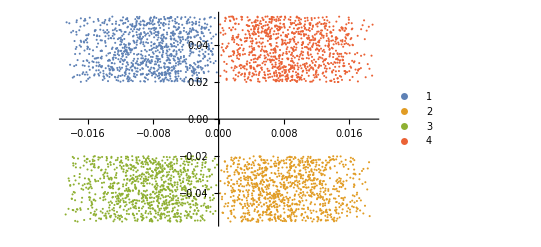

```mathematica
tryConstantes1[polo_]:=ReplaceAll[polo,{ql1->RandomReal[],ql2->RandomReal[],c1->RandomReal[{0,0.019}],c2->RandomReal[{0,0.019}],γp->RandomReal[{1/50,1/18}]}]
ListPlot[{ReIm[Table[tryConstantes1[polos[[1]]],1000]],ReIm[Table[tryConstantes1[polos[[2]]],1000]],ReIm[Table[tryConstantes1[polos[[3]]],1000]],ReIm[Table[tryConstantes1[polos[[4]]],1000]]},PlotLegends->{1,2,3,4}]
```

Vemos que, dado que los reales puros se ubicarían sobre las abcisas, no tenemos polos puramente reales si evaluamos la condición  . Por lo que, al menos mientras se cumpla esta condición, podemos aplicar el teorema del residuo sin incluir consideraciones adicionales. Si, en cambio, consideramos que  al asignar los valores, tenemos,

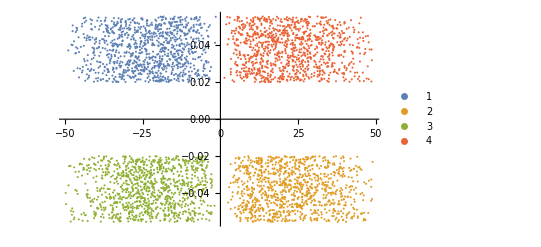

```mathematica
tryConstantes2[polo_]:=ReplaceAll[polo,{ql1->RandomReal[],ql2->RandomReal[],c1->RandomReal[{1,50}],c2->RandomReal[{1,50}],γp->RandomReal[{1/50,1/18}]}]
ListPlot[{ReIm[Table[tryConstantes2[polos[[1]]],1000]],ReIm[Table[tryConstantes2[polos[[2]]],1000]],ReIm[Table[tryConstantes2[polos[[3]]],1000]],ReIm[Table[tryConstantes2[polos[[4]]],1000]]},PlotLegends->{1,2,3,4}]
```

Conociendo los polos podemos calcular los residuos

```mathematica
residuos = Map[polo |->Residue[(c1^2 ql2^2+ql1^2 (γp^2+ω^2))/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4),{ω,polo}],polos]
```

{-(ⅈ (√c1 c2 ql1^2+c1^(3/2) ql2^2-2 ⅈ √c2 ql1^2 γp))/(8 √c2 √((√c1 √c2-ⅈ γp)^2) γp),(ⅈ √c1 c2 ql1^2+ⅈ c1^(3/2) ql2^2+2 √c2 ql1^2 γp)/(8 √c2 √((√c1 √c2-ⅈ γp)^2) γp),(ⅈ (√c1 c2 ql1^2+c1^(3/2) ql2^2+2 ⅈ √c2 ql1^2 γp))/(8 √c2 √((√c1 √c2+ⅈ γp)^2) γp),(-ⅈ √c1 c2 ql1^2-ⅈ c1^(3/2) ql2^2+2 √c2 ql1^2 γp)/(8 √c2 √((√c1 √c2+ⅈ γp)^2) γp)}

De acuerdo con los gráficos, los polos que estarían dentro de nuestro loop serían el 1 y el 4 y, por ende, los residuos que utilizaremos serán los asociados a estos dos polos. Entonces, la integral vendrá dada por

```mathematica
integral= FullSimplify[ⅈ (residuos[[1]]+residuos[[4]])]
```

((√c1 (c2 ql1^2+c1 ql2^2)-2 ⅈ √c2 ql1^2 γp)/(√((√c1 √c2-ⅈ γp)^2))+(√c1 (c2 ql1^2+c1 ql2^2)+2 ⅈ √c2 ql1^2 γp)/(√((√c1 √c2+ⅈ γp)^2)))/(8 √c2 γp)

Podemos simplificar esta expresión. Podemos decir que , pues ,  y  son números positivos. Luego,

```mathematica
((√c1 (c2 ql1^2+c1 ql2^2)-2 ⅈ √c2 ql1^2 γp)/(√c1 √c2-ⅈ γp)+(√c1 (c2 ql1^2+c1 ql2^2)+2 ⅈ √c2 ql1^2 γp)/(√c1 √c2+ⅈ γp))/(8 √c2 γp);
```

```mathematica
((√c1 (c2 ql1^2+c1 ql2^2)-2 ⅈ √c2 ql1^2 γp)/(√c1 √c2-ⅈ γp)+(√c1 (c2 ql1^2+c1 ql2^2)+2 ⅈ √c2 ql1^2 γp)/(√c1 √c2+ⅈ γp))/(8 √c2 γp)//FullSimplify
```

(c1 c2 ql1^2+c1^2 ql2^2+2 ql1^2 γp^2)/(4 c1 c2 γp+4 γp^3)

```mathematica
(ql1^2(c1 c2 +2  γp^2))/(4 (c1 c2 γp+ γp^3))+ (c1^2 ql2^2)/(4 (c1 c2 γp+4 γp));
```

#### Para B.

```mathematica
p3 = Expand[(-c2 ql1 ξl1+ql2 ξl2 (γp+ⅈ ω))/(c1 c2+(γp+ⅈ ω) (γp+ⅈ ω))]
```

-(c2 ql1 ξl1)/(c1 c2+(γp+ⅈ ω)^2)+(ql2 γp ξl2)/(c1 c2+(γp+ⅈ ω)^2)+(ⅈ ql2 ξl2 ω)/(c1 c2+(γp+ⅈ ω)^2)

```mathematica
p4 = Expand[(-c2 ql1 ξl1'+ql2 ξl2' (γp-ⅈ ω))/(c1 c2+(γp-ⅈ ω) (γp-ⅈ ω))]
```

-(c2 ql1 ξl1')/(c1 c2+(γp-ⅈ ω)^2)+(ql2 γp ξl2')/(c1 c2+(γp-ⅈ ω)^2)-(ⅈ ql2 ω ξl2')/(c1 c2+(γp-ⅈ ω)^2)

```mathematica
pb = Expand[p3 p4]
```

(c2^2 ql1^2 ξl1 ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))-(c2 ql1 ql2 γp ξl2 ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))-(ⅈ c2 ql1 ql2 ξl2 ω ξl1')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))-(c2 ql1 ql2 γp ξl1 ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(ql2^2 γp^2 ξl2 ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(ⅈ c2 ql1 ql2 ξl1 ω ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))+(ql2^2 ξl2 ω^2 ξl2')/((c1 c2+(γp-ⅈ ω)^2) (c1 c2+(γp+ⅈ ω)^2))

```mathematica
ReplaceAll[pb,{ξl2 ξl1'-> 0,ξl1 ξl2'-> 0}]//FullSimplify
```

(c2^2 ql1^2 ξl1 ξl1'+ql2^2 ξl2 (γp^2+ω^2) ξl2')/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4)

```mathematica
ReplaceAll[(c2^2 ql1^2 ξl1 ξl1'+ql2^2 ξl2 (γp^2+ω^2) ξl2')/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4),{ξl1 ξl1' ->1, ξl2 ξl2'-> 1}]
```

(c2^2 ql1^2+ql2^2 (γp^2+ω^2))/((c1 c2+γp^2)^2+2 (-c1 c2+γp^2) ω^2+ω^4)

Como esta expresión es similar, salvo por el hecho de que los subíndices están intercambiados, se espera que, sin pérdida de generalidad, tengamos que